```mathematica
(* Method of moments estimator *)
(*Function to generate rate matrix from an edge list and weights*)RateMatrix[edges_List,weights_List,n_Integer]:=Module[{Q},Q=ConstantArray[0,{n,n}];
Do[Q[[edges[[i,1]],edges[[i,2]]]]=weights[[i]],{i,Length[edges]}];
Do[Q[[i,i]]=-Total[Q[[i,All]]],{i,n}];
Q];

(*Function to compute steady-state probabilities*)SteadyStateProbabilities[Q_]:=Module[{n,A,b,π},n=Length[Q];
A=Append[Transpose[Q],ConstantArray[1,n]];
b=Append[ConstantArray[0,n],1];
π=LinearSolve[A,b];
π];

(*Function to compute mean first passage times*)
MeanFirstPassageTimes[Q_]:=Module[{n,Z,T},n=Length[Q];
ss = SteadyStateProbabilities[Q];
Pss = Table[ss, {i,n}];
Z=Inverse[Pss-Q]-Pss;
T=Table[(Z[[j,j]]-Z[[i,j]])/ss[[j]],{i,n},{j,n}];
Simplify[T]];

MeanFirstPassageTimes2[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-ConstantArray[1,n-1];(*-1 vector*)(*Solve Qsub x=-1*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[T];];

VarianceFirstPassageTimes[Q_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
m = MeanFirstPassageTimes2[Q];
T=ConstantArray[0,{n,n}];(*to hold T_{i->j} for i,j=1..n*)
Do[If[i==j,(*If same state,MFPT=0 by definition*)
T[[i,j]]=0,(*Else i!=j,solve the submatrix system:*)
subIdxs=Delete[Range[n],j];(*The set of states except j*)
Qsub=Q[[subIdxs,subIdxs]];(*Q^(j):remove row j,col j*)
rhs=-2*m[[subIdxs,j]];(*-1 vector*)(*Solve Qsub x=-2m*)
x=LinearSolve[Qsub,rhs];
(*x maps subIdxs->T_{(subIdxs)->j}.We want the entry for i.*)
T[[i,j]]=x[[First@Position[subIdxs,i]]] - m[[i,j]]^2;],{i,1,n},{j,1,n}];
Return[T];];

LaplaceTransformFPT[Q_,s_]:=Module[{n,T,subIdxs,Qsub,rhs,x},n=Length[Q];
T=ConstantArray[0,{n,n}];
(*T[[i,j]] will store phi_{i->j}(s)=E[e^{-s T_{i->j}}].*)Do[If[i==j,(*By definition,time from j to j is 0=>Laplace transform=E[e^{-s*0}]=1*)
T[[i,j]]=1,(*i!=j:solve the submatrix system (Q+sI)_{S' x S'}*phi_{S'}=-Q_{S',j},using the boundary condition phi_j(s)=1.*)
subIdxs=Delete[Range[n],j];(*states except j*)
Qsub=Q[[subIdxs,subIdxs]]-s*IdentityMatrix[n-1];
(*Build the inhomogeneous RHS=-Q[i,j],for each i in subIdxs*)rhs=Table[-Q[[subIdxs[[row]],j]],{row,1,n-1}];
x=LinearSolve[Qsub,rhs];
(*x gives phi_{k->j}(s) for k in subIdxs.We want the component corresponding to i.*)T[[i,j]]=x[[First@Position[subIdxs,i]]];],{i,1,n},{j,1,n}];
Return[FullSimplify[T]];];

LaplaceTransformToSetByState[Q_,start_,hit_List,s_]:=Module[{n=Length[Q],subStates,m,results,eqMatrix,eqRHS,hj,sol,iPos},(*If'start' is already in'hit',then the time is 0 with prob=1=>transform=1,but specifically we don't "hit h_j first" if j!=that state.We'll handle it below.*)If[MemberQ[hit,start],(*Then we trivially return a vector of dimension Length[hit],where the entry for'start' is 1,and all others 0.*)
Return[Map[If[#==start,1,0]&,hit]]];
(*Otherwise,we solve one linear system for each h_j in'hit'.*)
subStates=Complement[Range[n],hit];(*non-absorbing set*)m=Length[subStates];
results=Table[((*Build the (Q-sI) submatrix for non-absorbing states.*)eqMatrix=Table[Q[[subStates[[i]],subStates[[j]]]],{i,m},{j,m}];
Do[eqMatrix[[i,i]]-=s,{i,1,m}];
(*RHS=-Q_{i,h_j},for each i in subStates.*)
eqRHS=Table[-Q[[subStates[[i]],hj]],{i,1,m}];
(*Solve and get phi_i^(j)(s).Then extract the'start' component.*)
sol=LinearSolve[eqMatrix,eqRHS];
iPos=First@Position[subStates,start];
sol[[iPos]]),{hj,hit}  (*for each absorbing state in'hit'*)];
Return[results];];

LogSpecificity[c_,ω_,γ_,rates_,edges_]:= Module[{n,Q, weights,ss,kboff,konb,kuon,kbon,koffu,kuoff},
{kboff,konb,kuon,kbon,koffu,kuoff} = Table[rates[[i]][[1]]/.rates[[i]],{i,1,Length[rates]}];
weights={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb};
Q = RateMatrix[edges, weights,6];
ss = SteadyStateProbabilities[Q];
Log[ss[[3]]/ss[[5]]] + Log[ω/γ]
]
```

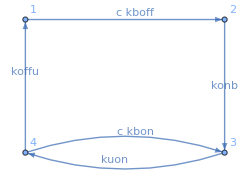

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Pure ligand, 1 binding site ***)

(*Edge lists and weights*)
edges1={{1,2},{2,3},{3,4},{4,3},{4,1}};
weights1={c*kboff,konb,kuon,c*kbon,koffu};
nstates1 = 4;
nedges1 = 5;

(*Plot the circuit*)
edgeList=Table[edges1[[i,1]]->edges1[[i,2]],{i,1,nedges1}];
g=Graph[edges1,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights1)[[i]],0.55],{i,1,nedges1}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{4,1},{3,2}}}]
```

```mathematica
Q1= RateMatrix[edges1, weights1, nstates1];
ss1 = SteadyStateProbabilities[Q1];

(*Mean first passage times*)
meanToff=MeanFirstPassageTimes2[Q1][[1,3]][[1]];
meanTon = MeanFirstPassageTimes2[Q1][[3,1]][[1]];
tau = meanToff + meanTon;

(*Variance of first passage times*)
varToff = FullSimplify[VarianceFirstPassageTimes[Q1][[1,3]]][[1]][[1]];
varTon = FullSimplify[VarianceFirstPassageTimes[Q1][[3,1]]][[1]][[1]];
```

```mathematica
(*Validating the Laplace transform FPT means and variances*)
Foff = LaplaceTransformFPT[Q1,s1][[1,3]][[1]];
Fon = LaplaceTransformFPT[Q1,s2][[3,1]][[1]];
meanToffLt = FullSimplify[-With[{s1=0},Evaluate[D[Foff,{s1,1}]]]];
meanTonLt = FullSimplify[-With[{s2=0},Evaluate[D[Fon,{s2,1}]]]];
varToffLt = FullSimplify[With[{s1=0},Evaluate[D[Foff,{s1,2}]]]-meanToffLt^2];
varTonLt = FullSimplify[With[{s2=0},Evaluate[D[Fon,{s2,2}]]]-meanTonLt^2];

On[Assert];
Assert[meanToffLt==meanToff]
Assert[meanTonLt==meanTon]
Assert[varToffLt==varToff]
Assert[varTonLt==varTon]
```

```mathematica
(*MM estimators*)
cHatOff = c/.Solve[meanToff==sampleToff,c][[1]];
cHatOn = c/.Solve[meanTon==sampleTon,c][[1]];

(*Variances of estimators*)
VarCHatOff = Simplify[With[{sampleToff = meanToff}, Evaluate[D[cHatOff, {sampleToff,1}]^2]]*varToff];
VarCHatOn = Simplify[With[{sampleTon = meanTon}, Evaluate[D[cHatOn, {sampleTon,1}]^2]]*varTon];
```

```mathematica
(*Concentration-rescaled Fisher information rates*)
dotFoff = FullSimplify[c^2 / (tau*VarCHatOff)];
dotFon = FullSimplify[c^2 / (tau*VarCHatOn)];
dotF = dotFoff + dotFon;
```

```mathematica
FullSimplify[dotFoff]
```

(c kboff koffu konb^3 kuon)/((c^2 kboff^2+konb^2) (c kboff (c kbon+koffu) konb+koffu konb kuon+c kboff (koffu+konb) kuon))

```mathematica
(*Maximize Fisher information rate*)
NMaximize[{With[{c=50},Evaluate[dotFoff]],0<kboff<0.0888,0<konb<5,0<kuon<5,0<kbon<0.0888,0<koffu<5 },{kboff,konb,kuon,kbon,koffu}]
```

{0.8,{kboff→0.05,konb→5.,kuon→5.,kbon→-9.9875×10^-9,koffu→5.}}

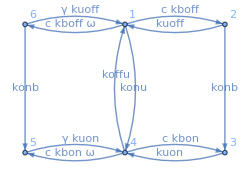

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},{4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,ω*c*kboff,γ*kuoff,c*kbon,kuon,ω*c*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
offStates = {6,1,2};
onStates = {5,4,3};
F1off = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = F1off[[3]][[1]]*F31 +F1off[[2]][[1]]*F41 + F1off[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];

(*Covariance matrix*)
Σx = Simplify[{{varToffLt,covTonToff},{covTonToff,varTonLt}},assum];
```

```mathematica
(*MM estimators*)
cHatOffSym =Simplify[c/.Solve[meanToffLt==sampleToff,c][[1]],assum];
cHatOnSym = FullSimplify[c/.Solve[meanTonLt==sampleTon,c][[2]],assum];

(*Jacobian*)
dcHatOff=Simplify[With[{sampleToff=meanToffLt},Evaluate[D[cHatOffSym, {sampleToff,1}]]],assum];
dcHatOn=Simplify[With[{sampleTon=meanTonLt},Evaluate[D[cHatOnSym, {sampleTon,1}]]],assum];
delf = {{dcHatOff,0},{0,dcHatOn }};
```

```mathematica
(*Covariance matrix of estimators*)
Σy = delfᵀ.Σx.delf;
```

```mathematica
(*Combined estimator and its variance*)
σ2off = Σy[[1,1]];
σ2on = Σy[[2,2]];
Cov = Σy[[1,2]];

cHat = (cHatOffSym*(σ2on-Cov) + cHatOnSym*(σ2off-Cov))/(σ2off + σ2on - 2Cov);
σ2 = (σ2on*σ2off - Cov^2)/(σ2off + σ2on - 2Cov);

(*Concentration-rescaled Fisher information rates*)
Foff = c^2/ (τ*σ2off);
Fon = c^2/ (τ*σ2on);
Fcomb = c^2/ (τ*σ2);
F[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[Fcomb];
G[c_,ω_,γ_,lnkboff_,lnkonb_,lnkuon_,lnkbon_,lnkoffu_,lnkuoff_,lnkonu_]:=F[c,ω,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]]
```

```mathematica
lnkmin = -5;
lnkmax = Log[5];
lnkdifflim = Log[0.0888];
cvals = Table[10.^x, {x,Subdivide[-2,4,15]}];
G[50,0,10,lnkdifflim, lnkmax,lnkmax,lnkmin,lnkmax,lnkmin,lnkmin]
```

0.664904

```mathematica
(*Maximize*)
rates = NMaximize[{G[c,ω,γ,lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu]/.{c->50,ω->0,γ->10,lnkonu->-5},lnkmin<lnkboff<lnkdifflim,
lnkmin<lnkonb<lnkmax,
lnkmin<lnkuon<lnkmax,
lnkmin<lnkbon<lnkdifflim,
lnkmin<lnkoffu<lnkmax,
lnkmin<lnkuoff<lnkmax},
{lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff},
Method->"DifferentialEvolution"]
```

{0.785192,{lnkboff→-2.99748,lnkonb→1.60944,lnkuon→1.60944,lnkbon→-5.,lnkoffu→1.60944,lnkuoff→-5.}}

```mathematica
(*Maximize Fisher information rate*)
kmin = 0.00001;
kmax = 5;
kdifflim = 0.0888;
cvals = Table[10.^x, {x,Subdivide[-1.5,2.5,1]}];
wvals = Table[10.^x, {x,Subdivide[-2,2.5,1]}];
results = Table[NMaximize[{With[{c=x, ω=y,γ=10},Evaluate[F]],kmin<kboff<kdifflim,kmin<konb<kmax,kmin<kuon<kmax,kmin<kbon<kdifflim,kmin<koffu<kmax,kmin<kuoff<kmax,kmin<konu<kmax },{kboff,konb,kuon,kbon,koffu,kuoff,konu}],{x, cvals},{y,wvals}];
```

```mathematica
(*Saving data*)
file = FileNameJoin[{$HomeDirectory},".julia/dev/LLROpt/mathematica-nbs/data/20250324/max-F-vs-c-vs-w.wl"]
Save[file, results]
```

/home/tohme/.julia/dev/LLROpt/mathematica-nbs/data/20250324/max-F-vs-c-vs-w.wl

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*** Tests ***)

pathList = {{1,3},{3,1},{1,5},{5,1},{4,5},{5,4}};

(*Mean first passage times*)
M2 = MeanFirstPassageTimes2[Q2];
meanTs = Table[M2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Variance of first passage times*)
V2 = VarianceFirstPassageTimes[Q2];
varTs = Table[V2[[pathList[[i,1]],pathList[[i,2]]]][[1]][[1]],{i,1,6}];
```

```mathematica
(*Laplace*)
F2= LaplaceTransformFPT[Q2,s];
laplaceTs = Table[F2[[pathList[[i,1]],pathList[[i,2]]]][[1]],{i,1,6}];

(*Check that mean Ton and var Ton from both methods agree*)
dF = Table[With[{s=0}, Evaluate[D[Fij, {s,1}]]],{Fij,laplaceTs}];
d2F = Table[With[{s=0}, Evaluate[D[Fij, {s,2}]]],{Fij,laplaceTs}];
```

```mathematica
varsLt = Table[d2F[[i]] - dF[[i]]^2,{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[-dF[[i]]] == FullSimplify[meanTs[[i]]]],{i,1,6}];
```

```mathematica
Do[Assert[FullSimplify[Expand[varsLt[[i]]]] == FullSimplify[Expand[varTs[[i]]]]],{i,1,6}];
```

```mathematica
(*Comparing with built-in functions*)
mproc1 = ContinuousMarkovProcess[1,Q2];
mproc3 = ContinuousMarkovProcess[3,Q2];
mproc4 = ContinuousMarkovProcess[4,Q2];
mproc5 = ContinuousMarkovProcess[5,Q2];
```

```mathematica
dist13 = FirstPassageTimeDistribution[mproc1,3];
dist15 = FirstPassageTimeDistribution[mproc1,5];

dist31 = FirstPassageTimeDistribution[mproc3,1];
dist41 = FirstPassageTimeDistribution[mproc4,1];
dist51 = FirstPassageTimeDistribution[mproc5,1];
distToff = FirstPassageTimeDistribution[mproc1,{3,4,5}];

meanTonBuiltin = (ss2[[2]]*Q2[[2,3]]*Mean[dist31]+ ss2[[1]]*Q2[[1,4]]*Mean[dist41]+ ss2[[6]]*Q2[[6,5]]*Mean[dist51])/(ss2[[2]]*Q2[[2,3]]+ss2[[6]]*Q2[[6,5]]+ss2[[1]]*Q2[[1,4]]);
FullSimplify[meanTonBuiltin]
```

(konu (konb+kuoff) kuon γ (konb+kuoff γ)+c^2 kboff kbon konb (γ+ω) (konb+kuoff γ+(konb+kuoff) ω)+c (kbon konu (konb+kuoff) (konb+kuoff γ) (γ+ω)+kboff konb ((koffu+kuon) γ (konb+kuoff γ)+(konb+kuoff) (koffu+kuon γ) ω)))/(koffu kuon γ (konu (konb+kuoff) (konb+kuoff γ)+c kboff konb (konb+kuoff γ+(konb+kuoff) ω)))

```mathematica
FullSimplify[meanTonLt]
```

(konu (konb+kuoff) kuon γ (konb+kuoff γ)+c^2 kboff kbon konb (γ+ω) (konb+kuoff γ+(konb+kuoff) ω)+c (kbon konu (konb+kuoff) (konb+kuoff γ) (γ+ω)+kboff konb ((koffu+kuon) γ (konb+kuoff γ)+(konb+kuoff) (koffu+kuon γ) ω)))/(koffu kuon γ (konu (konb+kuoff) (konb+kuoff γ)+c kboff konb (konb+kuoff γ+(konb+kuoff) ω)))

```mathematica
meanToffBuiltin = FullSimplify[Mean[distToff]]
```

((c kboff+konb+kuoff) (konb+kuoff γ)+c kboff (konb+kuoff) ω)/(konu (konb+kuoff) (konb+kuoff γ)+c kboff konb (konb+kuoff γ+(konb+kuoff) ω))

```mathematica
FullSimplify[meanToffLt]
```

((c kboff+konb+kuoff) (konb+kuoff γ)+c kboff (konb+kuoff) ω)/(konu (konb+kuoff) (konb+kuoff γ)+c kboff konb (konb+kuoff γ+(konb+kuoff) ω))

```mathematica
(*evaluating at the beginning*)
meanTonLtNoω = Simplify[With[{ω=0,konu=0},Evaluate[meanTonLt]],assum]
```

(c kbon+koffu+kuon)/(koffu kuon)

```mathematica
cHatOnSymNoω = FullSimplify[c/.Solve[meanTonLtNoω==sampleTon,c][[1]],assum]
```

-(koffu+kuon-koffu kuon sampleTon)/kbon

```mathematica
dcHatOnSymNoω = FullSimplify[D[cHatOnSymNoω,sampleTon],assum]
```

(koffu kuon)/kbon

```mathematica
FullSimplify[With[{sampleTon = meanTonLtNoω},Evaluate[dcHatOnSymNoω]],assum]
```

(koffu kuon)/kbon

```mathematica
(*evaluating at the end*)
cHatOnSymSimpl = Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[cHatOnSym]],assum]
```

1/2 (-2-konu+sampleTon-√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
meanTonSimpl = Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[meanTonLt]]]
```

(c^2+konu+c (2+konu))/(c+konu)

```mathematica
Simplify[c/.Solve[meanTonSimpl==sampleTon,c][[2]],assum]
```

1/2 (-2-konu+sampleTon+√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
Simplify[With[{sampleTon=meanTonSimpl},Evaluate[%]],assum]
```

c

```mathematica
dcHatOnSym = Simplify[D[cHatOnSym,sampleTon],assum];
Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[dcHatOnSym]],assum]
```

(2-konu-sampleTon+√(konu^2+(-2+sampleTon)^2+2 konu sampleTon))/(2 √(konu^2+(-2+sampleTon)^2+2 konu sampleTon))

```mathematica
dcHatOnSymEndEval = Simplify[With[{sampleTon=meanTonLt},Evaluate[dcHatOnSym]],assum];
```

```mathematica
Simplify[With[{ω=0,kuoff=0,koffu=1,kbon=1,kboff=1,kuon=1},Evaluate[dcHatOnSymEndEval]]]
```

konu/(c^2+konu+2 c konu+konu^2)

```mathematica
(*Computing the exact MLE variance*)
FOn=(ss2[[2]]*Q2[[2,3]]*F31+ ss2[[1]]*Q2[[1,4]]*F41+ ss2[[6]]*Q2[[6,5]]*F51)/(ss2[[2]]*Q2[[2,3]]+ss2[[6]]*Q2[[6,5]]+ss2[[1]]*Q2[[1,4]]);
FOnNoω = Simplify[With[{ω=0,kuoff=0},Evaluate[FOn]],{}]
```

(koffu (c kboff kuon+konu (kuon+s2)))/((c kboff+konu) (koffu (kuon+s2)+s2 (c kbon+kuon+s2)))

```mathematica
(*-4 koffu kuon+(c kbon+koffu+kuon)^2*) (*c^2 kbon^2+(koffu-kuon)^2+2 c kbon (koffu+kuon)*)
(*{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}*)
POnNow[c] := Simplify[InverseLaplaceTransform[FOnNoω,s2,t2]]
```

```mathematica
POnNow[c]
```

(ⅇ^(-1/2 (c kbon+koffu+kuon+√(-4 koffu kuon+(c kbon+koffu+kuon)^2)) t2) koffu (c kbon konu-c ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t2) kbon konu+koffu konu-ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t2) koffu konu-2 c kboff kuon+2 c ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t2) kboff kuon-konu kuon+ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t2) konu kuon+konu √(-4 koffu kuon+(c kbon+koffu+kuon)^2)+ⅇ^(√(-4 koffu kuon+(c kbon+koffu+kuon)^2) t2) konu √(-4 koffu kuon+(c kbon+koffu+kuon)^2)))/(2 (c kboff+konu) √(-4 koffu kuon+(c kbon+koffu+kuon)^2))

```mathematica
FullSimplify[POnNow[c],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

(ⅇ^(-1/2 (B+√D) t2) ((B+√D+(-B+√D) ⅇ^(√D t2)) koffu konu+2 A (-1+ⅇ^(√D t2)) (c kboff+konu)))/(2 √D (c kboff+konu))

```mathematica
Expand[%]
```

-(A c ⅇ^(-1/2 (B+√D) t2) kboff)/(√D (c kboff+konu))+(A c ⅇ^(-1/2 (B+√D) t2+√D t2) kboff)/(√D (c kboff+konu))-(A ⅇ^(-1/2 (B+√D) t2) konu)/(√D (c kboff+konu))+(A ⅇ^(-1/2 (B+√D) t2+√D t2) konu)/(√D (c kboff+konu))+(ⅇ^(-1/2 (B+√D) t2) koffu konu)/(2 (c kboff+konu))+(B ⅇ^(-1/2 (B+√D) t2) koffu konu)/(2 √D (c kboff+konu))+(ⅇ^(-1/2 (B+√D) t2+√D t2) koffu konu)/(2 (c kboff+konu))-(B ⅇ^(-1/2 (B+√D) t2+√D t2) koffu konu)/(2 √D (c kboff+konu))

```mathematica
d2POnNow = FullSimplify[D[Log[POnNow[c]],{c,2}],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

$Aborted

```mathematica
integrand = FullSimplify[d2POnNow*POnNow[c],{D==-4 koffu kuon+(c kbon+koffu+kuon)^2,B==c kbon+koffu+kuon,A==koffu kuon}]
```

-(A ⅇ^(-1/2 (B+√D) t2) (-1+ⅇ^(√D t2)) kbon^2 (-4 (8 A+D)+8 A √D t2 Coth[(√D t2)/2]+D (4 A+D) t2^2 Csch[(√D t2)/2]^2))/(4 D^(5/2))

```mathematica
With[{konu=0},Evaluate[integrand]]
```

-(ⅇ^(-(B t2)/2) kboff s1 (4 c C kboff konb+2 C konb s1) Sinh[(√D t2)/2])/(c √D (c kboff+s1)^3 (konb+s1))

```mathematica
(*Numerical equivalents*)
meanTonNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[meanTonLt];
meanToffNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[meanToffLt];
varTonNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[varTonLt];
varToffNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[varToffLt];
covTonToffNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_] := Evaluate[covTonToff];
dcHatOffNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_,sampleToff_]:= Evaluate[dcHatOffSym];
dcHatOnNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_,sampleTon_]:= Evaluate[dcHatOnSym];
cHatOffNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_,sampleToff_]:= Evaluate[cHatOffSym];
cHatOnNum[c_,ω_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_,sampleTon_]:= Evaluate[cHatOnSym];

(*Numeric function for Fisher info rate*)
Fnum[c_?NumericQ,ω_?NumericQ,γ_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ] :=Module[{meanTon, meanToff, varTon, varToff, covTonToff,dcHatOn,dcHatOff,delf,Σx,Σy,τ,σ2off,σ2on,σ2,Cov,cHat,Foff,Fon,F},

(*Numerical values for mean, variance and cov of FPTs*)
meanTon = meanTonNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu];
meanToff = meanToffNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu];
varTon = varTonNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu];
varToff = varToffNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu];
covTonToff = covTonToffNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu];
τ = meanTon + meanToff;

Σx = {{varToff,covTonToff},{covTonToff,varTon}};

(*Jacobian*)
dcHatOff=dcHatOffNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu,meanToff];
dcHatOn=dcHatOnNum[c,ω,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu,meanTon];
delf = {{dcHatOff,0},{0,dcHatOn }};

(*Covariance matrix of estimators*)
Σy = delfᵀ.Σx.delf;

(*Combined estimator and its variance*)
σ2off = Σy[[1,1]];
σ2on = Σy[[2,2]];
Cov = Σy[[1,2]];

(*cHat = (cHatOff*(σ2on-Cov) + cHatOn*(σ2off-Cov))/(σ2off + σ2on - 2Cov)*);
σ2 = (σ2on*σ2off - Cov^2)/(σ2off + σ2on - 2Cov);

(*Concentration-rescaled Fisher information rates*)
(*Foff = c^2/ (τ*σ2off);
Fon = c^2/ (τ*σ2on);*)
F = c^2/ (τ*σ2);

Return[F]]
```